# Fourier Plots - General examples

## The plots below comes from the data extract in the name.cpp files. Each section will represent one specific code

## fourier_F.cpp analysis

### Plotting of the Gaussians

```mathematica
σ = 0.1;
```

General::munfl: Exp[-1799.88] is too small to represent as a normalized machine number; precision may be lost.

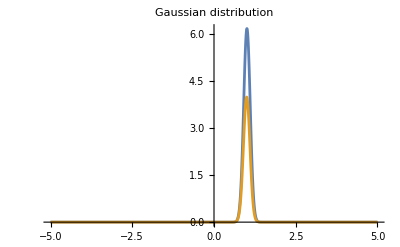

```mathematica
Plot[{Cosh[x]*1/(σ √(2 π))Exp[(-(x- 1)^2)/(2 σ^2)],1/(σ √(2 π))Exp[(-(x-1)^2)/(2 σ^2)]},{x,-5,5},PlotLabel->"Gaussian distribution",PlotRange->All]
```

```mathematica
FourierTransform[1/(σ √(2 π))Exp[-x^2/(2 σ^2)],x,ω]
```

0.398942 ⅇ^(-0.005 ω^2)

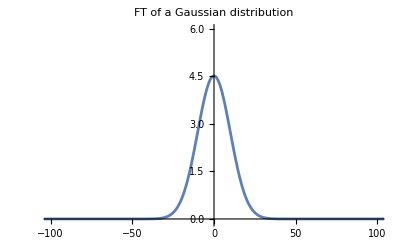

```mathematica
Plot[11.3*0.398942 ⅇ^(-0.005000000000000001 ω^2),{ω,-146.96938456699067,146.96938456699067},PlotLabel->"FT of a Gaussian distribution", PlotRange -> {{-100,100},{-0.1,6}}]
```

```mathematica
Clear[col1]
Clear[col2]
```

```mathematica
data = Import[NotebookDirectory[]<>"gaussian_F.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

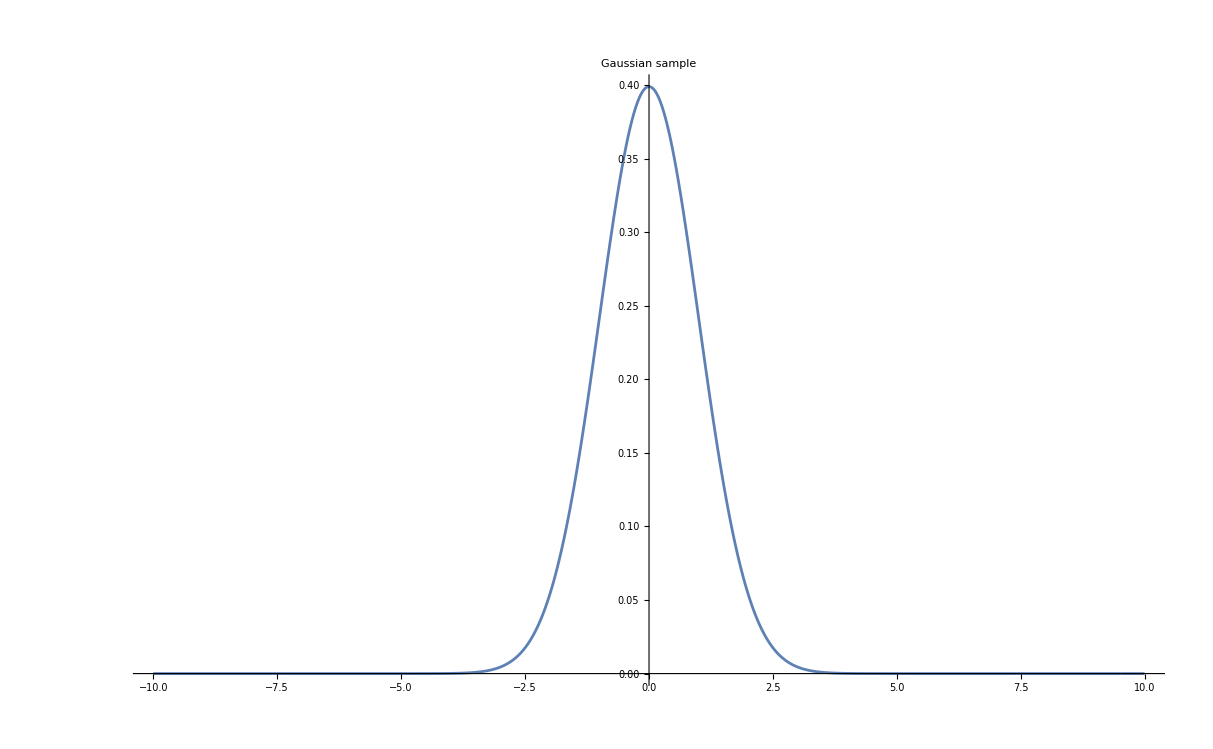

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Gaussian sample", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_F.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

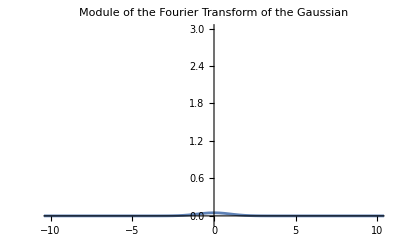

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Module of the Fourier Transform of the Gaussian", PlotRange -> {{-10,10},{-0.1,3}}]
```

### Over the normalisation

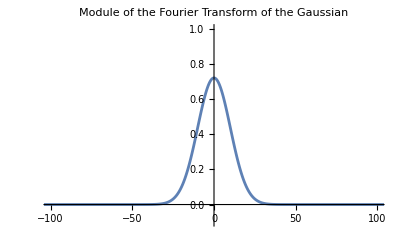

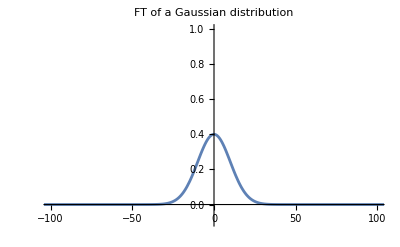

```mathematica
ListLinePlot[Transpose[{col1,0.159*col2}],PlotLabel->"Module of the Fourier Transform of the Gaussian", PlotRange -> {{-100,100},{-0.1,1}}]
Plot[0.398942 ⅇ^(-0.005000000000000001 ω^2),{ω,-146.96938456699067,146.96938456699067},PlotLabel->"FT of a Gaussian distribution", PlotRange -> {{-100,100},{-0.1,1}}]
```

## fourier_table_FT.cpp analysis

### data_table.dat plotting

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"data_table.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

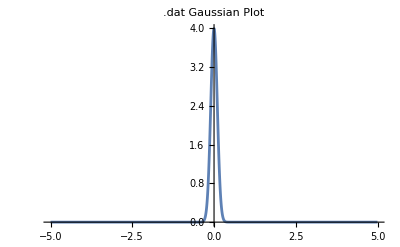

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->".dat Gaussian Plot", PlotRange ->All]
```

### Output files

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"function_FT.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

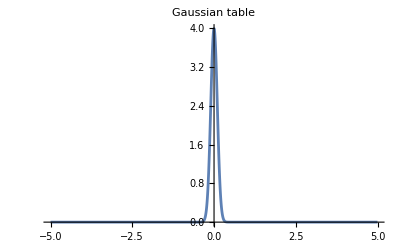

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Gaussian table", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_FT.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

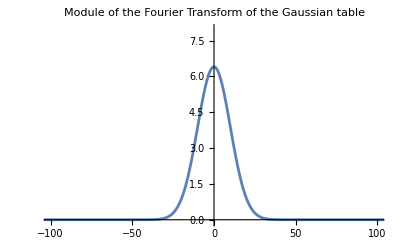

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Module of the Fourier Transform of the Gaussian table", PlotRange -> {{-100,100},{-0.1,8}}]
```

## fourier_newexp_FNE.cpp analysis

### Plotting

### Output files

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_sech_FNE.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

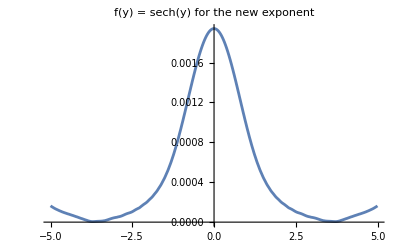

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"f(y) = sech(y) for the new exponent", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_gaussian_FNE.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

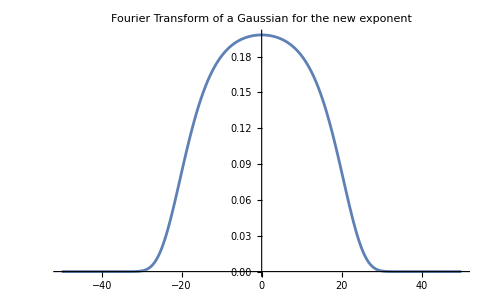

```mathematica
ListLinePlot[10*Transpose[{col1,col2}],PlotLabel->"Fourier Transform of a Gaussian for the new exponent", PlotRange -> All]
```

General::munfl: Exp[-2499.8] is too small to represent as a normalized machine number; precision may be lost.

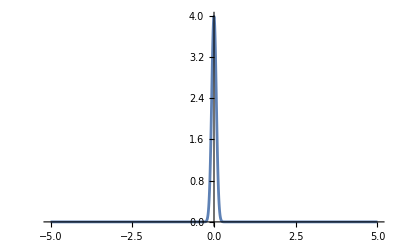

General::munfl: Exp[-550387.] is too small to represent as a normalized machine number; precision may be lost.

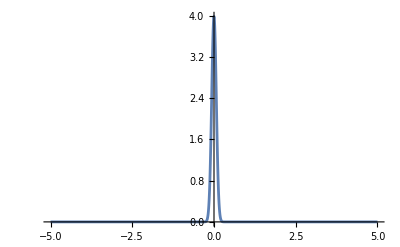

```mathematica
Plot[1/(0.1*√(2 π))Exp[-x^2/0.1^2],{x,-5,5},PlotRange->All]
Plot[1/(0.1*√(2 π))Exp[(-(Sinh[x])^2)/(0.1*0.1)],{x,-5,5},PlotRange->All]
```

```mathematica
FourierTransform[Sech[x],x,w]
```

√(π/2) Sech[(π w)/2]

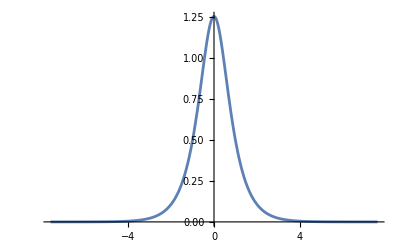

```mathematica
Plot[√(π/2) Sech[(π w)/2],{w,-7.639437268410977,7.639437268410977},PlotRange->All]
```

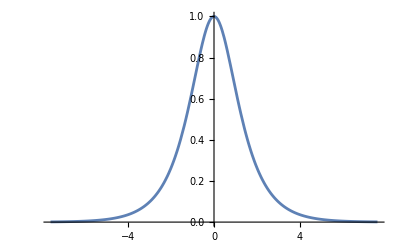

```mathematica
Plot[Sech[w],{w,-7.639437268410977,7.639437268410977},PlotRange->All]
```

## fourier_newexp_PDF_FNEPDF.cpp

### PDF

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

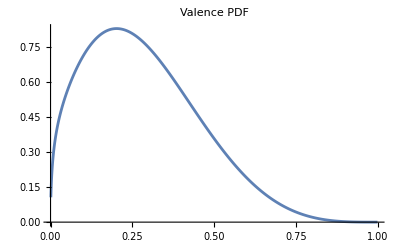

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence PDF", PlotRange->All]
```

### PDF-Fourier

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_FNEPDF.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

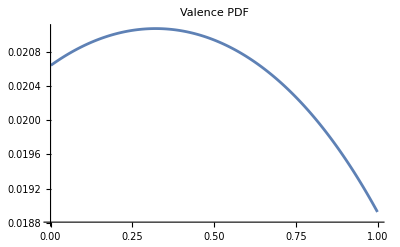

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence PDF", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"magnitude_wj_FNEPDF.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

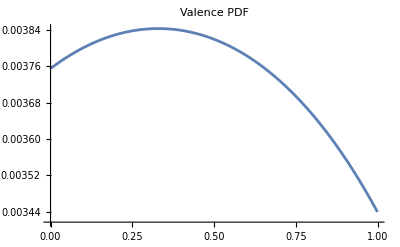

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence PDF", PlotRange->All]
```

### TEST

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence PDF", PlotRange->All]
```

-Graphics-

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

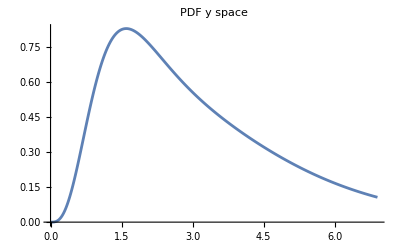

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Y_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

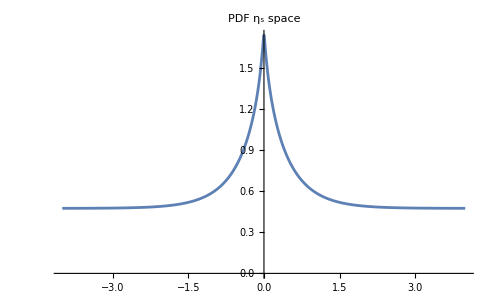

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"YY_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

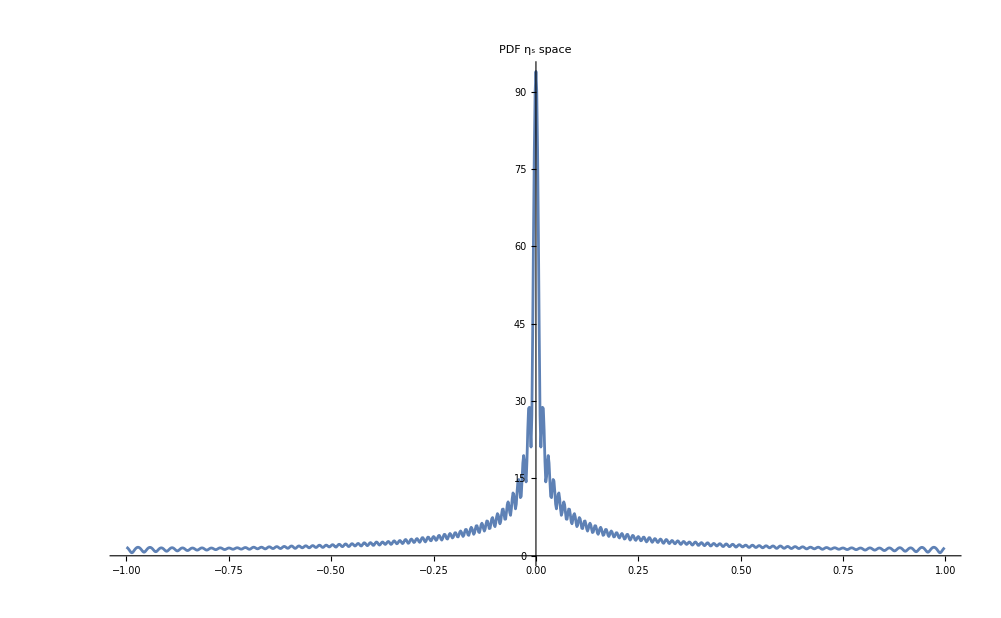

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

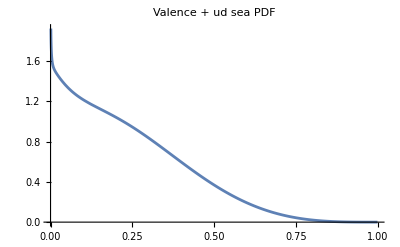

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence + ud sea PDF", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

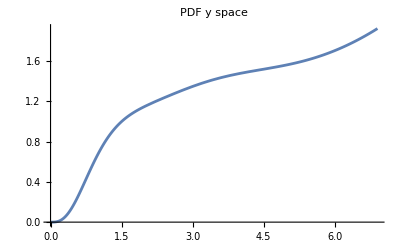

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Y1_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

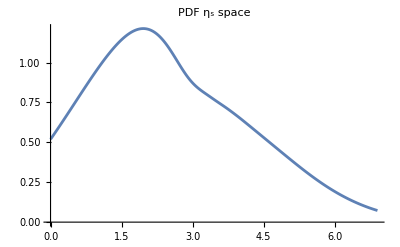

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"YY1_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

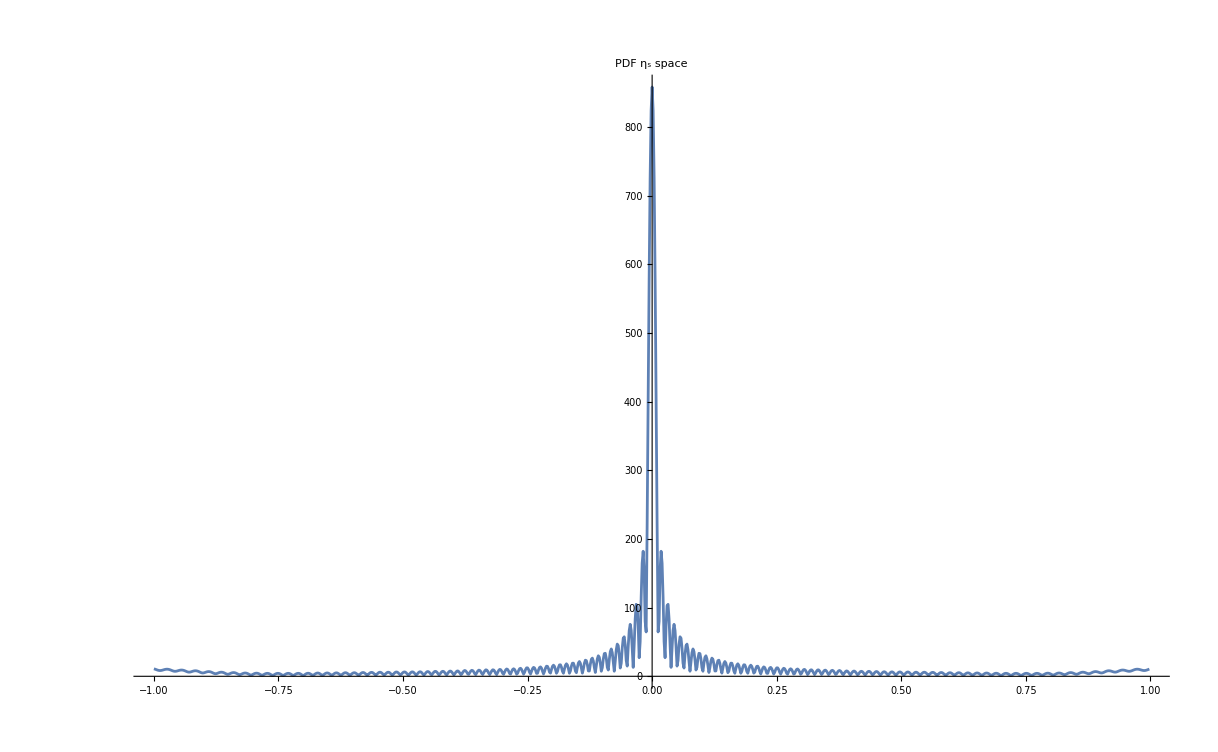

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence_ud_sea_udsscc.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

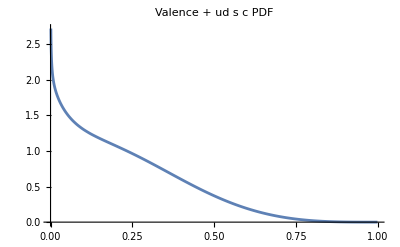

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Valence + ud s c PDF", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

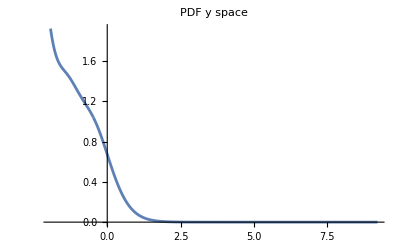

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Y_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

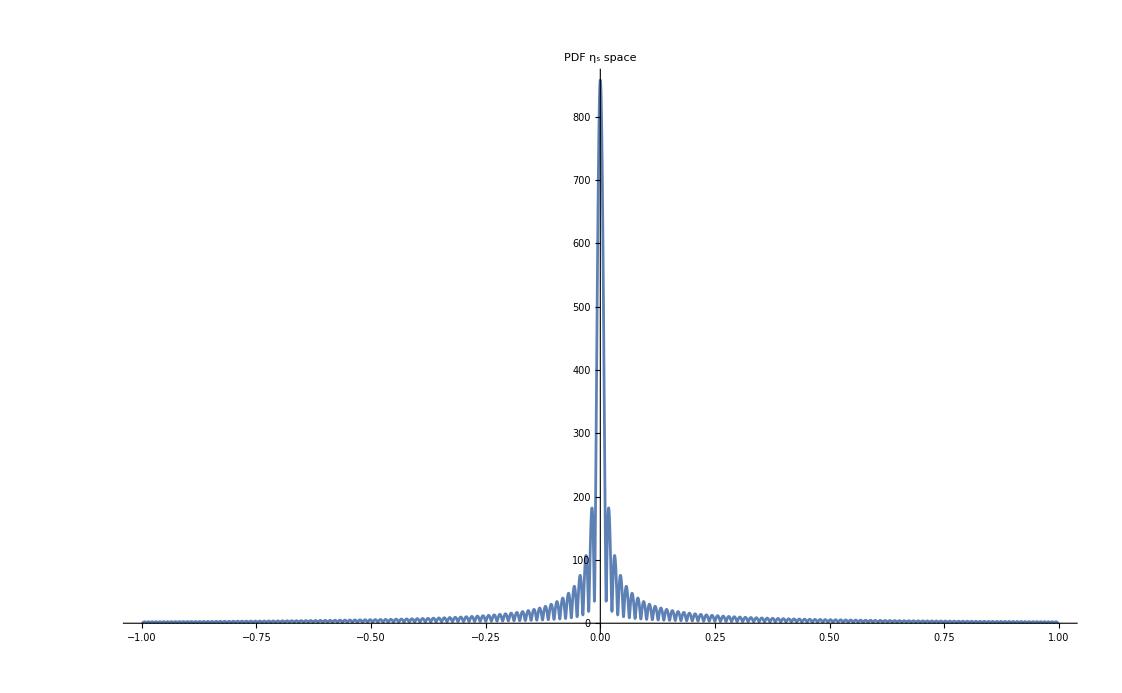

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

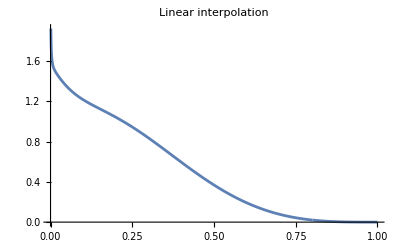

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Linear interpolation", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

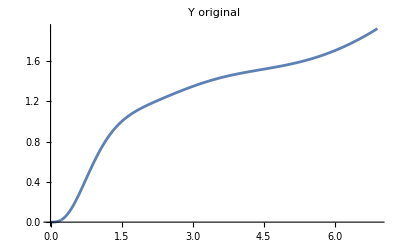

```mathematica
ListLinePlot[Transpose[{-Log[col1],col2}],PlotLabel->"Y original", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"interp.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

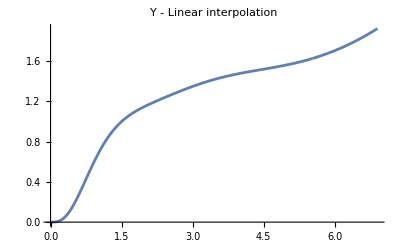

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Y - Linear interpolation", PlotRange->All]
```

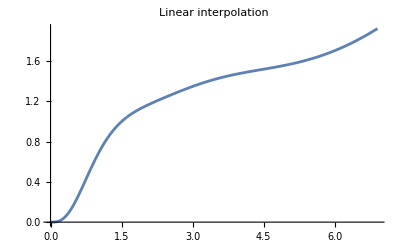

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
col1=data[[All,1]];
col2=data[[All,2]];
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"Linear interpolation", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Y_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

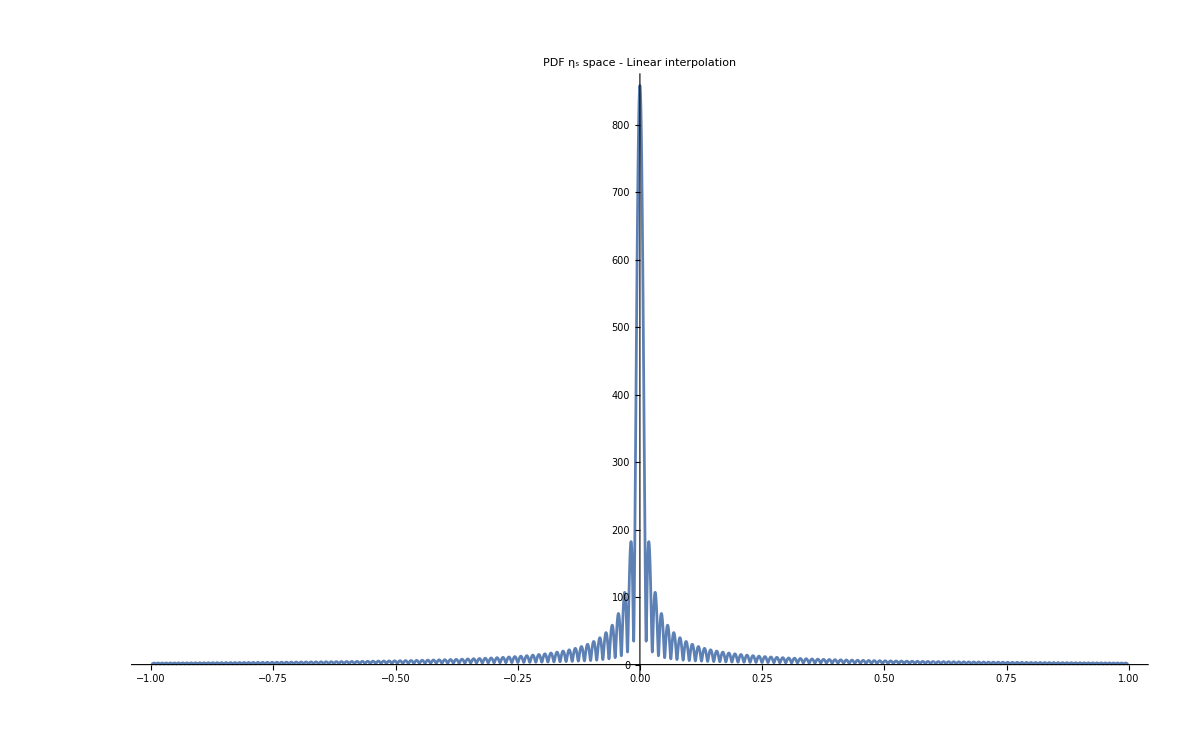

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF η_s space - Linear interpolation", PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

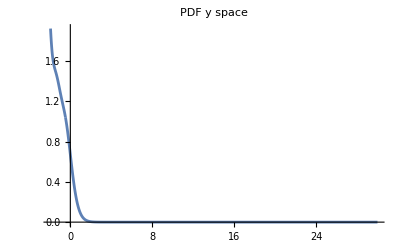

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space", PlotRange->All]
```